```mathematica
Get[NotebookDirectory[]<>#]&/@
{
"combine_packages.wls",
"load_takahashi_data.wl"
};
```

```mathematica
figureNameSteadyStates1D="steady_states_1D";
figureDirectorySteadyStates1D=figureNameSteadyStates1D;
figureDirectorySteadyStates1Dsensitivity = figureDirectorySteadyStates1D<>"/sensitivity";
```

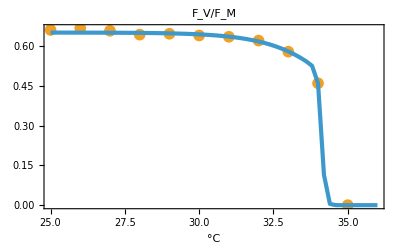

```mathematica
(Export[NotebookDirectory[]<>"export/steady-state-data-1D-FvFm-temperature.pdf",#];#)&@Show[
ListPlot[Normal[data["FigS1"][Select[#["h"]==0.5&]][All,{#["temp"],#["Fv/Fm"]}&]],
imageSizePadding[ImagePaddingXunits],PlotMarkers->plotMarkers,AxesOrigin->{Automatic},PlotStyle->{{Dashed,colorPoints,thickness}},Joined->False,style],
makeOneSimulationSteadyStatePlot[Join[{L->0},pars[-6]],w,wRange1D,{FvFm},24 3600,{PlotStyle->{{colorCurves,thickness}}}]
(*Plot[FvFmBase(rT/(rT+xT))/.{parsPre},{w,25,36},PlotStyle->{{Darker@Gray,thickness}},Evaluate@style]*),PlotRange->All,FrameLabel->{{None,None},{w/.units,None}},PlotLabel->"F_V/F_M"]
```

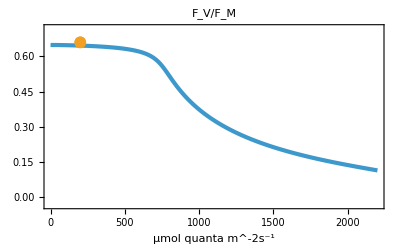

```mathematica
(Export[NotebookDirectory[]<>"export/steady-state-data-1D-FvFm-light.pdf",#];#)&@Show[
ListPlot[{Join[{200},Normal@data["FigS1"][Select[#["h"]==0.5∧#["temp"]==25.&]][All,"Fv/Fm"]]},
imageSizePadding[ImagePaddingXunits],PlotMarkers->plotMarkers,PlotRange->{{Lrange[[1]],Lrange[[2]]},{FvFmMinPlot,FvFmMaxPlot}},PlotStyle->{{Dashed,colorPoints,thickness}},Joined->False,style],
makeOneSimulationSteadyStatePlot[pars[-6],L,Lrange,{FvFm},24 3600,{PlotStyle->{{colorCurves,thickness}},PlotRange->{{Lrange[[1]],Lrange[[2]]},{FvFmMinPlot,FvFmMaxPlot}}}],
PlotRange->{All,{FvFmMinPlot,FvFmMaxPlot}},FrameLabel->{{None,None},{L/.units,None}},PlotLabel->"F_V/F_M"]
```

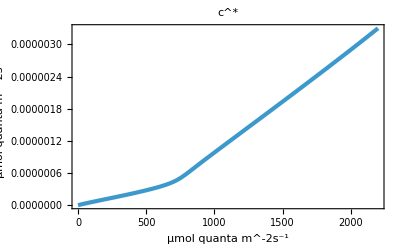

```mathematica
makeOneSimulationSteadyStatePlot[pars[-6],L,Lrange,{#},24 3600,{PlotLabel->#/.names}]&@cX
```

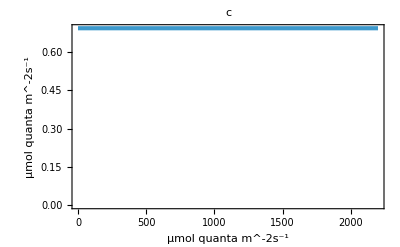
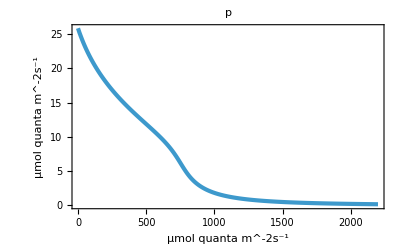
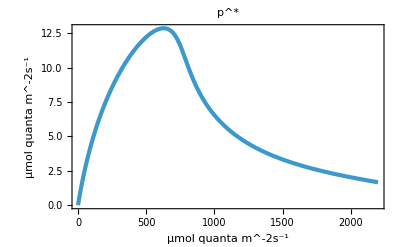
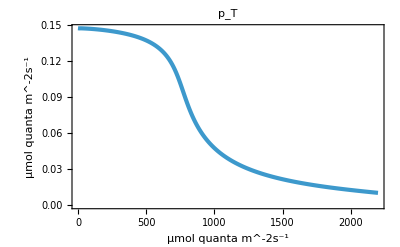
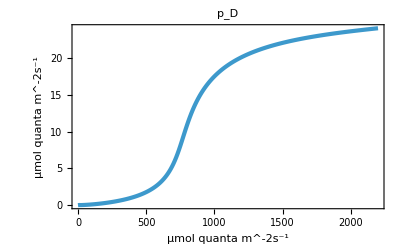
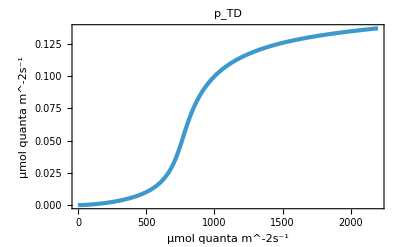
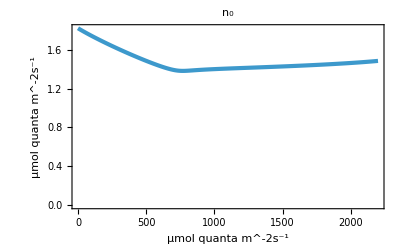
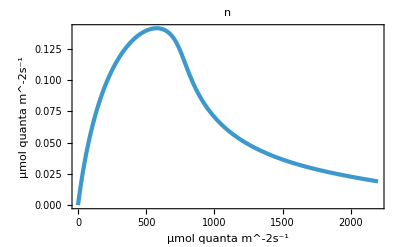
-Graphics--Graphics-
-Graphics--Graphics-
-Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics-
-Graphics--Graphics-

```mathematica
(Export[NotebookDirectory[]<>"export/"<>figureDirectorySteadyStates1D<>"/"<>figureNameSteadyStates1D<>"-light.pdf",#];#)&@GridMap[makeOneSimulationSteadyStatePlot[pars[-6],L,Lrange,{#},24 3600,{PlotLabel->#/.names}]&,quants]
```

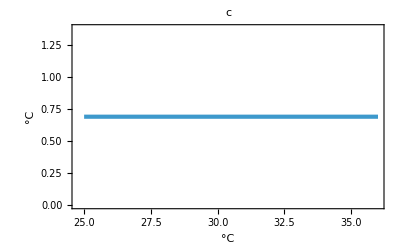
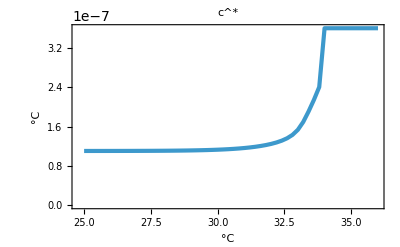
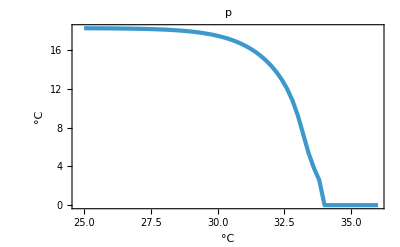
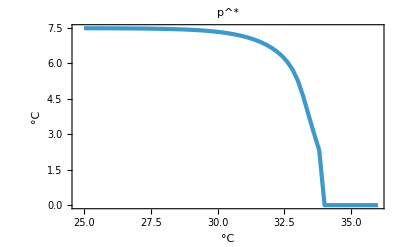
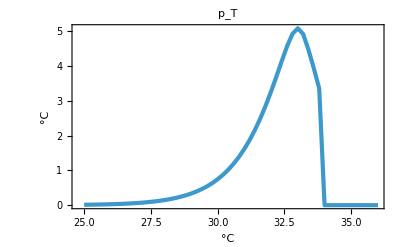
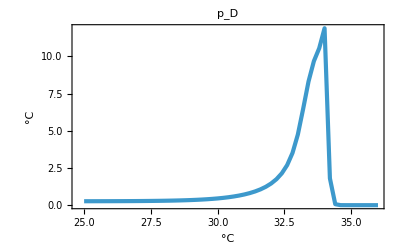
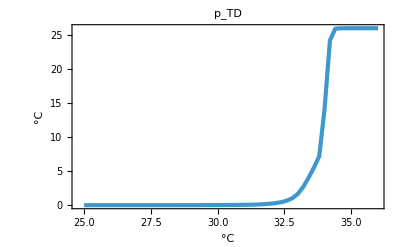
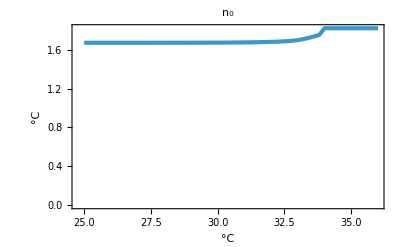

```mathematica
(Export[NotebookDirectory[]<>"export/"<>figureDirectorySteadyStates1D<>"/"<>figureNameSteadyStates1D<>"-temperature.pdf",#];#)&@GridMap[makeOneSimulationSteadyStatePlot[pars[-6],w,wRange1D,{#}, 24 3600,{PlotRange->Full,AxesOrigin->{Automatic,0},PlotLabel->#/.names}]&,quants]
```

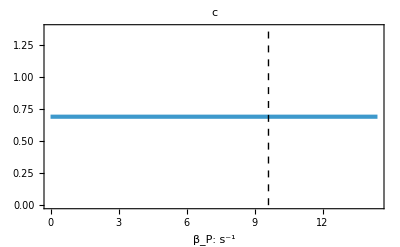
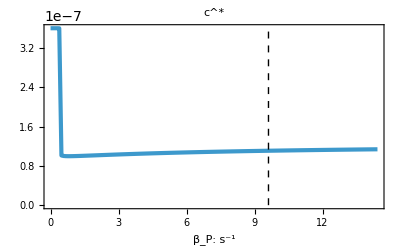
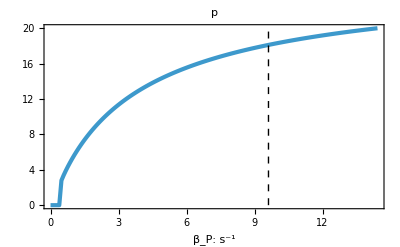
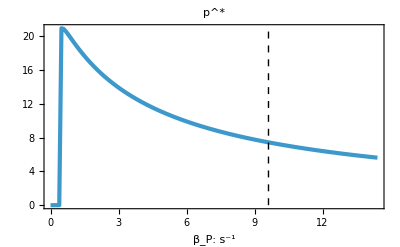
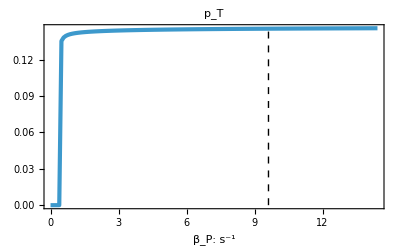
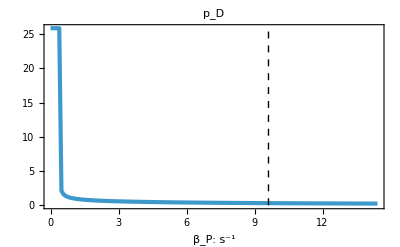
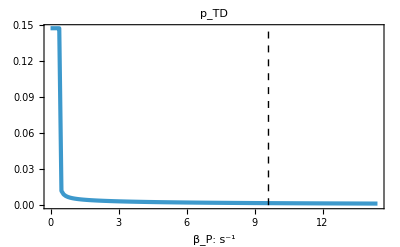
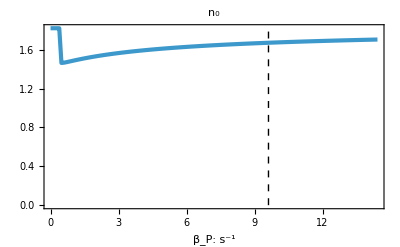

```mathematica
(Export[NotebookDirectory[]<>"export/"<>figureDirectorySteadyStates1Dsensitivity<>"/"<>figureNameSteadyStates1D<>"-betaP.pdf",#];#)&@GridMap[makeOneSimulationSteadyStatePlot[pars[-6],βP,Table[i βP/.pars[0],{i,0,1.5,.01}],{#}, 24 3600,{FrameLabel->{{None,None},{"β_P: s^-1",None}},Epilog->{Black,Dashed,Line[{{βP/.pars[0],0},{βP/.pars[0],10^5}}]},PlotRange->Full,AxesOrigin->{Automatic,0},PlotLabel->#/.names}]&,quants]
```